```mathematica
(*Testing for Fixed Grid Size with in the panel*)
Panel[GraphicsGrid[Table[Table[Placeholder[],{78}(*No Of Columns*)],{48}(*No Of Rows*)],Spacings-> {0,0},ImageSize-> {780,480},Background-> LightBlue],ImageSize-> {780,480},Alignment-> {Center,Center}]
```

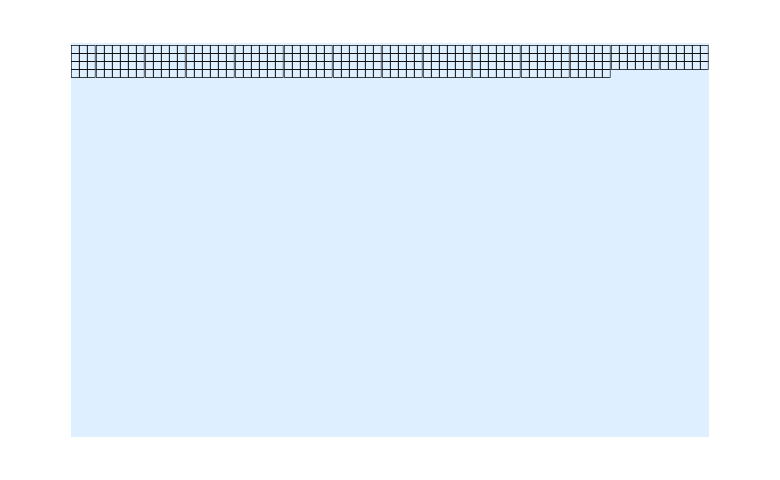
```mathematica
-Graphics-
(*Sucess*)
```

```mathematica
(*Replace the "Button" instead of "PlaceHolder" in the above test *)
Panel[GraphicsGrid[Table[Table[Button["Click",""],{78}(*No Of Columns*)],{48}(*No Of Rows*)],Spacings-> {.2,0.4},ImageSize-> {780,480}],ImageSize-> {780,480},Alignment-> {Center,Center}]
```

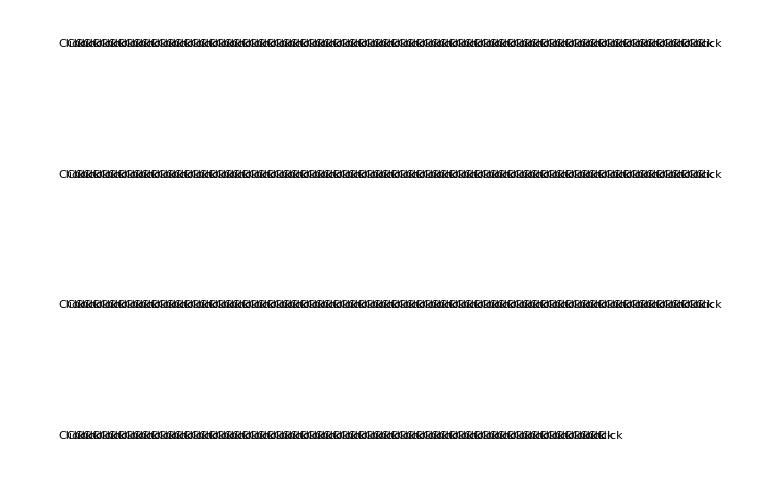
```mathematica
-Graphics-

(*Fail*)
```

```mathematica
(*Test for Grid without fixing the size in the panel*)
Panel[Grid[Table[Table[Button["Click",""],{78}(*No Of Columns*)],{48}(*No Of Rows*)],Spacings-> {.315,0.4},ItemSize-> {0,0}],ImageSize-> {780,480},Alignment-> {Center,Center}]
```

```mathematica
{{"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}, {"Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click", "Click"}}

(*Fail*)
```

```mathematica
(*Test for spanning with in grid which has already been generated*)
duplicateGrid=GraphicsGrid[Table[Table[Placeholder[],{78}(*No Of Columns*)],{48}(*No Of Rows*)]];
grid=(
(*Variable Initialization*)

noOfRows=Length[FullForm[duplicateGrid][[1,1,2]]];(*No of Rows in Grid*)
noOfColumns=Length[FullForm[duplicateGrid][[1,1,2,1]]];(*No of columns in Grid*)
buttonPosition={5,7};(*Positions of the controls*)
rowSpaning=15;(*No of rows spanning for the specific control*)
columnSpaning=15;(*No of columns spanning for the specific control*)
noOfControls=Placeholder[];
result={};(*This is final result but at the starting time it is empty*)
(*Coding Is start from here*)

For[row=1,row≤noOfRows,row++,
individualRow={};
   (For[col=1,col≤noOfColumns,col++,             
 (   If[row==buttonPosition[[1]](*here it checks control Row position*),
(*True Condition*)
      (If[col==buttonPosition[[2]],
      (individualRow=Append[individualRow,noOfControls];),
       If[col≤(buttonPosition[[2]]+rowSpaning),
           If[col>buttonPosition[[2]],
              (individualRow=Append[individualRow,SpanFromLeft];),
               (individualRow=Append[individualRow,1];)
              ],
           (individualRow=Append[individualRow,1];)
         ]
    ];
      ),
(*False Condition*)
If[row>buttonPosition[[1]],
    If[row≤(buttonPosition[[1]]+rowSpaning),       
        (If[col==buttonPosition[[2]],
         (individualRow=Append[individualRow,SpanFromAbove];),
          If[col≤(buttonPosition[[2]]+columnSpaning),
               If[col>buttonPosition[[2]],
                    (individualRow=Append[individualRow,SpanFromBoth];),
                    (individualRow=Append[individualRow,1];)
                  ],
              (individualRow=Append[individualRow,1];)
            ]
         ];
         ),
      (individualRow=Append[individualRow,1];)
   ],(individualRow=Append[individualRow,1];)
   ]
 ];
 )
        ];)(*Main Foor loop body ended here*)
result=Append[result,individualRow];
   ];
Panel[GraphicsGrid[result,Frame-> None,Spacings-> {0,0},ImageSize-> {780,480},Background-> LightBlue],ImageSize-> {790,490},Alignment-> {Center,Center}])
```

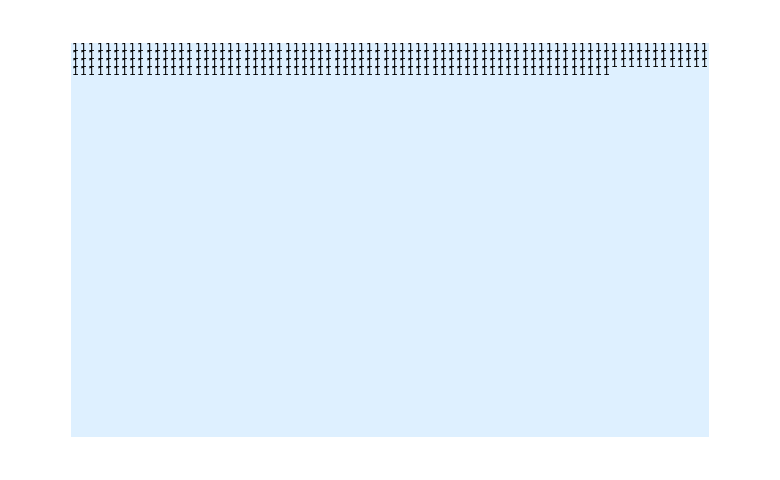
```mathematica
-Graphics-
(*Fail*)
```

```mathematica
(*Test for grid Fullform*)
h=Grid[{{1,2,3},{4,5,6}}];
Length[FullForm[hj][[1,1,2]]]
```

48

```mathematica
(*Sucess*)
```

```mathematica
(*I am Assigning grid to the variable hj*)
hj=GraphicsGrid[Table[Table[Placeholder[],{78}(*No Of Columns*)],{48}(*No Of Rows*)],Spacings-> {0,0},ImageSize-> {780,480},Background-> LightBlue]
```

```mathematica
-Graphics-
(*Fail*)
```

```mathematica
(*Testing if graphicsgrid can be spanned after it has been created with smaller graphicsgrid*)
testGrid[g11_,g12_,g13_,g21_,g22_,g23_,g31_,g32_,g33_]:=GraphicsGrid[{{g11,g12,g13},{g21,g22,g23},{g31,g32,g33}},Spacings-> {0,0},ImageSize-> {90,90}]
a1="Row 1";
a2=SpanFromLeft;
a3=SpanFromLeft;
a4=SpanFromLeft;
a5=Button["test","",ImageSize->{90,30}];
a6=SpanFromLeft;
a7="Row3";
a8="test1";
a9="x";
testGrid[a1,a2,a3,a4,a5,a6,a7,a8,a9]
```

-Graphics-

```mathematica
a1="Row 2"
```

Row 2

```mathematica
-Graphics-
(*Success*)
```

```mathematica
(*Testing if graphicsgrid accepts lists as an argument*)
testGrid1[row1_,row2_,row3_]:=GraphicsGrid[{row1,row2,row3},Spacings-> {0,0},ImageSize-> {90,90},Frame-> All]
Row2={SpanFromAbove,SpanFromBoth,SpanFromBoth};
Row1={Button["Test",""],SpanFromLeft,SpanFromLeft};
Row3={InputField[],SpanFromLeft,SpanFromLeft};
testGrid1[Row1,Row2,Row3]
```

-Graphics-

```mathematica
-Graphics-
(*Success*)
```

```mathematica
Clear[k,g]
```

```mathematica
(*Testing a function whose output is k1i*)
KFunction[j_,i_]:=Subscript[g,j,i]
For[i=1,i≤ 48,i++,(Print[KFunction[1,i]])]
```

g_(1,1)

g_(1,2)

g_(1,3)

g_(1,4)

g_(1,5)

g_(1,6)

g_(1,7)

g_(1,8)

g_(1,9)

g_(1,10)

g_(1,11)

g_(1,12)

g_(1,13)

g_(1,14)

g_(1,15)

g_(1,16)

g_(1,17)

g_(1,18)

g_(1,19)

g_(1,20)

g_(1,21)

g_(1,22)

g_(1,23)

g_(1,24)

g_(1,25)

g_(1,26)

g_(1,27)

g_(1,28)

g_(1,29)

g_(1,30)

g_(1,31)

g_(1,32)

g_(1,33)

g_(1,34)

g_(1,35)

g_(1,36)

g_(1,37)

g_(1,38)

g_(1,39)

g_(1,40)

g_(1,41)

g_(1,42)

g_(1,43)

g_(1,44)

g_(1,45)

g_(1,46)

g_(1,47)

g_(1,48)

```mathematica
(*Success*)
```

```mathematica
(*Creating an Array with 78 variables*)
testArray=Array[KFunction,78]
```

```mathematica
{Subscript[k, 1,1],Subscript[k, 1,2],Subscript[k, 1,3],Subscript[k, 1,4],Subscript[k, 1,5],Subscript[k, 1,6],Subscript[k, 1,7],Subscript[k, 1,8],Subscript[k, 1,9],Subscript[k, 1,10],Subscript[k, 1,11],Subscript[k, 1,12],Subscript[k, 1,13],Subscript[k, 1,14],Subscript[k, 1,15],Subscript[k, 1,16],Subscript[k, 1,17],Subscript[k, 1,18],Subscript[k, 1,19],Subscript[k, 1,20],Subscript[k, 1,21],Subscript[k, 1,22],Subscript[k, 1,23],Subscript[k, 1,24],Subscript[k, 1,25],Subscript[k, 1,26],Subscript[k, 1,27],Subscript[k, 1,28],Subscript[k, 1,29],Subscript[k, 1,30],Subscript[k, 1,31],Subscript[k, 1,32],Subscript[k, 1,33],Subscript[k, 1,34],Subscript[k, 1,35],Subscript[k, 1,36],Subscript[k, 1,37],Subscript[k, 1,38],Subscript[k, 1,39],Subscript[k, 1,40],Subscript[k, 1,41],Subscript[k, 1,42],Subscript[k, 1,43],Subscript[k, 1,44],Subscript[k, 1,45],Subscript[k, 1,46],Subscript[k, 1,47],Subscript[k, 1,48],Subscript[k, 1,49],Subscript[k, 1,50],Subscript[k, 1,51],Subscript[k, 1,52],Subscript[k, 1,53],Subscript[k, 1,54],Subscript[k, 1,55],Subscript[k, 1,56],Subscript[k, 1,57],Subscript[k, 1,58],Subscript[k, 1,59],Subscript[k, 1,60],Subscript[k, 1,61],Subscript[k, 1,62],Subscript[k, 1,63],Subscript[k, 1,64],Subscript[k, 1,65],Subscript[k, 1,66],Subscript[k, 1,67],Subscript[k, 1,68],Subscript[k, 1,69],Subscript[k, 1,70],Subscript[k, 1,71],Subscript[k, 1,72],Subscript[k, 1,73],Subscript[k, 1,74],Subscript[k, 1,75],Subscript[k, 1,76],Subscript[k, 1,77],Subscript[k, 1,78]}(*Success*)
```

```mathematica
(*Creating an Array with any number of variables*)
testArray1[l_]:=Array[KFunction,l];
testArray1[78]
```

{21,k_(1,2),k_(1,3),k_(1,4),k_(1,5),k_(1,6),k_(1,7),k_(1,8),k_(1,9),k_(1,10),k_(1,11),k_(1,12),k_(1,13),k_(1,14),k_(1,15),k_(1,16),k_(1,17),k_(1,18),k_(1,19),k_(1,20),k_(1,21),k_(1,22),k_(1,23),k_(1,24),k_(1,25),k_(1,26),k_(1,27),k_(1,28),k_(1,29),k_(1,30),k_(1,31),k_(1,32),k_(1,33),k_(1,34),k_(1,35),k_(1,36),k_(1,37),k_(1,38),k_(1,39),k_(1,40),k_(1,41),k_(1,42),k_(1,43),k_(1,44),k_(1,45),k_(1,46),k_(1,47),k_(1,48),k_(1,49),k_(1,50),k_(1,51),k_(1,52),k_(1,53),k_(1,54),k_(1,55),k_(1,56),k_(1,57),k_(1,58),k_(1,59),k_(1,60),k_(1,61),k_(1,62),k_(1,63),k_(1,64),k_(1,65),k_(1,66),k_(1,67),k_(1,68),k_(1,69),k_(1,70),k_(1,71),k_(1,72),k_(1,73),k_(1,74),k_(1,75),k_(1,76),k_(1,77),k_(1,78)}

```mathematica
Subscript[k,1,1]=21
```

21

```mathematica
Subscript[1,2]
```

1_2

```mathematica
LayoutGrid[m_,n_]:=Subscript[m,n]
```

```mathematica
CreateGrid[m_,n_]:=LayoutGrid[m,n]
```

```mathematica
CreateGrid[2,3]
```

2_3

```mathematica
(*Testing how list performs as an argument to Layout Function*)
list={a,2,3,4,5,6,7,8,9,10};
Function123[m_,n_,list_]:=(result1={};For[{i=1,k=1},i≤ m,i++,(individualRow={};For[j=1,j≤ n,{j++,k++},(individualRow=Append[individualRow,list[[k]]];)];result1=Append[result1,individualRow];)];GraphicsGrid[result1])
Function123[5,2,list]
```

-Graphics-

```mathematica
(*calling the Function123*)
```

```mathematica
Dynamic[Function123[5,2,list]]
```

```mathematica
a=20;
```

```mathematica
(*Success*)
```

```mathematica
(**)
Function123[m_,n_,list_]:=(result1={};For[{i=1,k=1},i≤ m,i++,(individualRow={};For[j=1,j≤ n,{j++,k++},(individualRow=Append[individualRow,list[[k]]];)];result1=Append[result1,individualRow];)];GraphicsGrid[result1])
CreateGrid[rows_,columns_]:=(individualColumn={};For[i=1,i≤rows,i++,(For[j=1,j≤ columns,j++,(individualColumn=Append[individualColumn,Subscript[grid,i,j]];)];)];individualColumn)
```

```mathematica
Dynamic[CreateGrid[3,4]]
```

```mathematica
(*Make the values like G1,1.....to Gm,n*)
Values[m_,n_]:=Subscript[G,m,n]
```

```mathematica
Table[Subscript[G,i,j],{i,1,3},{j,1,4}]
```

{{G_(1,1),G_(1,2),G_(1,3),G_(1,4)},{G_(2,1),G_(2,2),G_(2,3),G_(2,4)},{G_(3,1),G_(3,2),G_(3,3),G_(3,4)}}

```mathematica
(*Testing for getting the options for Button*)
button=Button[Style["Click",Bold,30,White],"",Background-> Blue,ImageSize-> {180,60}]
Options[button,ImageSize]
```

Click

{ImageSize→{180,60}}

```mathematica
(*Success*)
```

```mathematica
(*Again i am trying button with in the MouseAppearance*)
button1=MouseAppearance[Button[Style["Click",Bold,30,White],"",Background-> Blue,ImageSize-> {180,60}],"LinkHand"];
Options[button1]
{}
(*Fail*)
```

```mathematica
Clear[CreateGrid]
```

```mathematica
Clear[rows,column,Ele]
```

```mathematica
(*I am just creating the function for grid*)
createGrid[rows_,column_]:=(finalRows={};For[i=1,i≤ rows,i++,(individualColumns={};For[j=1,j≤ column,j++,(individualColumns=Append[individualColumns,Subscript[Ele,i,j]];)];finalRows=Append[finalRows,individualColumns];)];GraphicsGrid[finalRows,ImageSize-> {1000,1000},Background-> LightBlue])
```

```mathematica
(*I Wrote a function CreateGrid and call that Function*)
createGrid[38,48]
```

```mathematica
(*The below code is StructuredLayout_GrandhiWOrkbook.nb*)
(*Function For Placing the Control*)
placeControl[controlRowPosition_,controlColumnPosition_,controlID_,controlWidthSize_,controlHeightSize_,list_]:=
(subScriptPositionOne=controlRowPosition/10;
subScriptPositionTwo=controlColumnPosition/10;
rowSpanning=controlWidthSize/10;
columnSpanning=controlHeightSize/10;
(*For[i=1,i≤48 ,i++,(For[j=1,j≤ 78,j++,(If[Subscript[e,i,j]==ToString[Subscript[e,i,j]],(Subscript[e,i,j]="")])])];*)
For[row=subScriptPositionOne,row≤(subScriptPositionOne+columnSpanning) ,row++,
       (If[row==subScriptPositionOne,
(*True Condition*)
          (For[column=subScriptPositionTwo,column≤ (subScriptPositionTwo+rowSpanning),column++,     (If[column==subScriptPositionTwo,(list[[row,column]]=controlID;),(list[[row,column]]=SpanFromLeft;)])]
       ),
(*False Condition*)
          (For[column=subScriptPositionTwo,column≤ (subScriptPositionTwo+rowSpanning),column++,     (If[column==subScriptPositionTwo,(list[[row,column]]=SpanFromAbove;),(list[[row,column]]=SpanFromBoth;)])]
       )])
    ];

)
(*Success*)
(*layoutGrid Function for making the Graphicsgrid*)
layoutGrid[list_]:=Panel[Grid[list,Background-> LightBlue,Spacings-> {0,0},ItemSize-> {0,0},Alignment-> {Center,Center}],ImageSize-> {780,480},Background-> LightBlue]
(*Success*)
(*Function For Creating the Graphicsgrid Elements*)
createGrid[rows_,column_]:=(list={};For[i=1,i≤ rows,i++,(individualColumns={};For[j=1,j≤ column,j++,(individualColumns=Append[individualColumns,""];)];list=Append[list,individualColumns];)];layoutGrid[list])
(*Sucess*)
(*Test For Calling the Functions*)
placeControl[400,600,Button[Style["Click",Bold,White],"",ImageSize-> {180,60},Background-> Blue],180,60,list]
(*Fail*)
(*Test For Calling the Functions*)
placeControl[200,300,PopupMenu[Dynamic[x],{1,2,3},ImageSize-> {180,60}],180,60,list]
(*Fail*)
(*Test For Calling the Functions*)
placeControl[100,600,PopupMenu[Dynamic[x],{1,2,3},ImageSize-> {180,60}],180,60,list]
(*Fail*)
(*Test For Calling the Functions*)
placeControl[10,50,Button[Style["Click",Bold,White],"",ImageSize-> {180,60},Background-> Blue],180,60,list]
(*Fail*)
(*Test For Calling the Functions*)
placeControl[200,100,Button[Style["Click",Bold,White],"",ImageSize-> {180,60},Background-> Blue],180,60,list]
(*Fail*)
Set::setps: "\!\({\(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\(« 44 »\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\)}\) in the part assignment is not a symbol."
Set::setps: "\!\({\(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\(« 44 »\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\)}\) in the part assignment is not a symbol."
Set::setps: "\!\({\(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\(« 44 »\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\), \(\({\"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \"\", \(\(« 28 »\)\)}\)\)}\) in the part assignment is not a symbol."
General::stop: "Further output of \!\(\*StyleBox[\(Set :: setps\), \"MessageName\"]\) will be suppressed during this calculation."
(*After Assigning all the controls and then finally cal the createGrid Function*)
Dynamic[createGrid[48,78]]

Subscript[f,2,3]=Button[Style["Click",Bold,White],"",ImageSize-> {180,60},Background-> Blue];
Subscript[e,2,3]
""
(*list Values*)
Dynamic[list]

(*Success*)
(*I am Just testing list changed or not*)
list[[1,2]]=10;
(*Success*)
(*Something testing on GraphicsGrid*)
grid=GraphicsGrid[{{1,2,3},{4,5,6}}];
FullForm[grid]
Graphics[List[List[],List[List[Inset[1,List[193.5,-192.],List[Center,Center],List[360.,360.]],Inset[2,List[580.5,-192.],List[Center,Center],List[360.,360.]],Inset[3,List[967.5,-192.],List[Center,Center],List[360.,360.]]],List[Inset[4,List[193.5,-576.],List[Center,Center],List[360.,360.]],Inset[5,List[580.5,-576.],List[Center,Center],List[360.,360.]],Inset[6,List[967.5,-576.],List[Center,Center],List[360.,360.]]]],List[]],Rule[PlotRangePadding,List[6,5]],Rule[ContentSelectable,True]]
grid1=Grid[{{1,2,3},{4,5,6},{7,8,9}}];
FullForm[grid1]
Grid[List[List[1,2,3],List[4,5,6],List[7,8,9]]]
(*Find the POsition of specific element in grid*)
Position[grid1,2]
{{1,1,2}}
(*Success*)
(*Again I make the grid with empty elements *)
grid2=Dynamic[Grid[{{"","",""},{"","",""}}]]
Position[grid2,""]

{{1,1,1,1},{1,1,1,2},{1,1,1,3},{1,1,2,1},{1,1,2,2},{1,1,2,3}}
(*Success*)
```

```mathematica
(*Testing For Placecontrol Function with overlapping code*)
placeControl[yCoOrdinate_,xCoOrdinate_,controlID_,controlWidth_,controlHeight_,list_,meshFactor_]:=
(rowNumber=yCoOrdinate/meshFactor;
columnNumber=xCoOrdinate/meshFactor;
rowSpan=controlWidth/meshFactor;
columnSpan=controlHeight/meshFactor;
updatedList={};For[i=1,i<= Length[list],i++,
          (individualRow={};
           For[j=1,j<= Length[list[[i]]],j++,
              (If[i==rowNumber,
                 (If[j==columnNumber,
                     (control=list[[i,j]];If[control==ToString[""],(individualRow=Append[individualRow,(list[[i,j]]=controlID)];For[k=(j+1),k<=(j+rowSpan),k++,(control1=list[[i,k]];If[control1==ToString[""],(individualRow=Append[individualRow,(list[[i,k]]=SpanFromLeft)];),(individualRow=Append[individualRow,list[[i,k]]];)])];j=(k-1);),(individualRow=Append[individualRow,(list[[i,j]]=control)];)];),
                     (individualRow=Append[individualRow,list[[i,j]]])
                    ]
                  ),
                 (If[((rowNumber<i)&&(i<=(rowNumber+columnSpan))),(If[j==columnNumber,(control2=list[[i,j]];If[control2==ToString[""],(individualRow=Append[individualRow,(list[[i,j]]=SpanFromAbove)];For[k=(j+1),k<=(j+rowSpan),k++,(individualRow=Append[individualRow,(list[[i,k]]=SpanFromBoth)];)];j=(k-1);),(individualRow=Append[individualRow,(list[[i,j]]=SpanFromAbove)];)]),(individualRow=Append[individualRow,control2])]),(individualRow=Append[individualRow,list[[i,j]]];)])
                 ]
               )
              ];
           updatedList=Append[updatedList,individualRow]
           )
         ];
updatedList
)
```

```mathematica
(*Success*)
```

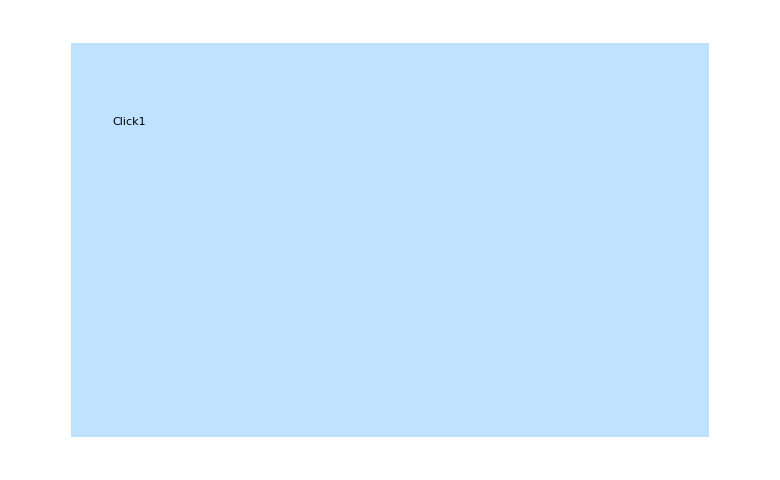

```mathematica
(*Calling the placeControl Function *)
testingList=ConstantArray["",{48,78}];
 testingList=Quiet[StructuredLayout`placeControl[100,60,Button["Click1","",Background-> Blue,ImageSize-> {180,60}],180,60,testingList,10]];
 testingList=Quiet[StructuredLayout`placeControl[150,70,Button["Click2","",Background-> Blue,ImageSize-> {180,60}],180,60,testingList,10]];
Panel[GraphicsGrid[testingList,ImageSize-> {780,480},Spacings-> {0,0},Background-> RGBColor[.745,.886,1],Alignment-> {Left,Top}],ImageSize-> {780,480},Background-> RGBColor[.745,.886,1]]
```

```mathematica
(*Fail Something logic was wrong in placecontrol Function*)
```